```mathematica
SetDirectory["~/Library/AFS@Reed/emcmanis/Thesis/TeX/Thesis Template/Figures"]
```

/afs/reed.edu/user/e/m/emcmanis/Thesis/TeX/Thesis Template/Figures

## Chapter 1

### Constants

```mathematica
h = 6.626*10^(-34); (*J s*)
hbar = h/(2π);
e=-1.602*10^(-19); (* C *)
ϵ0=8.854*10^(-12); (* C^2/(J m) *)
me=9.109*10^(-31); (*kg*)
mp=1.673*10^(-27); (*kg*)
μ=(mp/(me+mp))*me;
a0=(4π ϵ0 hbar^2)/(μ e^2);
```

### Bohr hydrogen energies

```mathematica
Ens=Table[-hbar^2/(a0^2 2 μ n^2)*1/(1.602*10^(-19)),{n,1,10}]
```

{-13.5941,-3.39852,-1.51045,-0.84963,-0.543763,-0.377613,-0.27743,-0.212408,-0.167828,-0.135941}

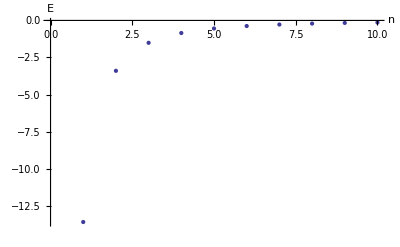

```mathematica
ListPlot[Ens, PlotRange->Full,AxesLabel->{"n", "E"}]
```

### Hydrogen Wave Functions

```mathematica
?LaguerreL
```

LaguerreL[n,x] gives the Laguerre polynomial L_n(x). 
LaguerreL[n,a,x] gives the generalized Laguerre polynomial L_n^a(x).

```mathematica
psi[n_,ρ_]:=(*n!*Sqrt[(2/(n a0))^3 ((n-1)!)/(2n(n!)^3)]*)ⅇ^-(ρ/(n))*LaguerreL[n-1,1,2*ρ/(n)]
```

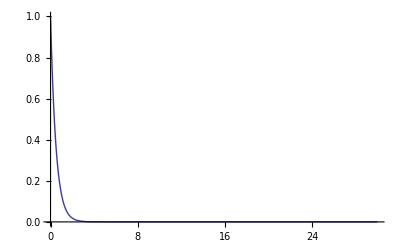

```mathematica
Plot[psi[1,r]^2,{r,0,30},PlotRange->All]
```

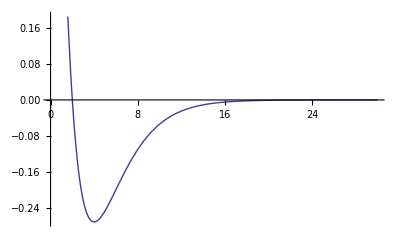

```mathematica
Plot[psi[2,r],{r,0,30}]
```

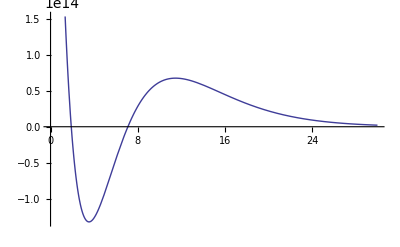

```mathematica
Plot[psi[3,r],{r,0,30}]
```

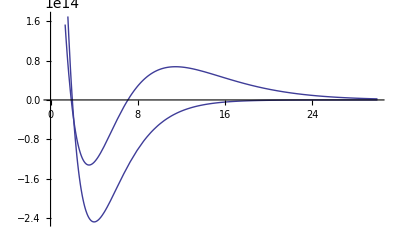

```mathematica
Show[%62,%63,%61]
```

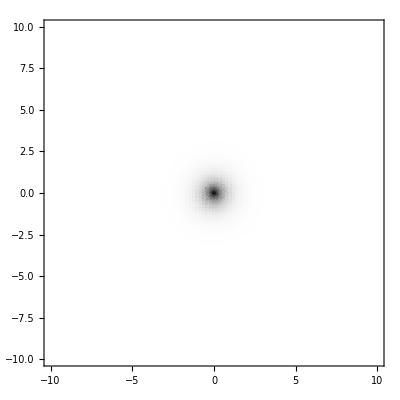

```mathematica
DensityPlot[(psi[1,Sqrt[x^2+y^2]])^2,{x,-10,10},{y,-10,10},PlotRange->{0,1},PlotPoints->100,ColorFunction -> Function[{z}, GrayLevel[1-z]], ColorFunctionScaling -> True, MaxRecursion -> 10]
```

#### test

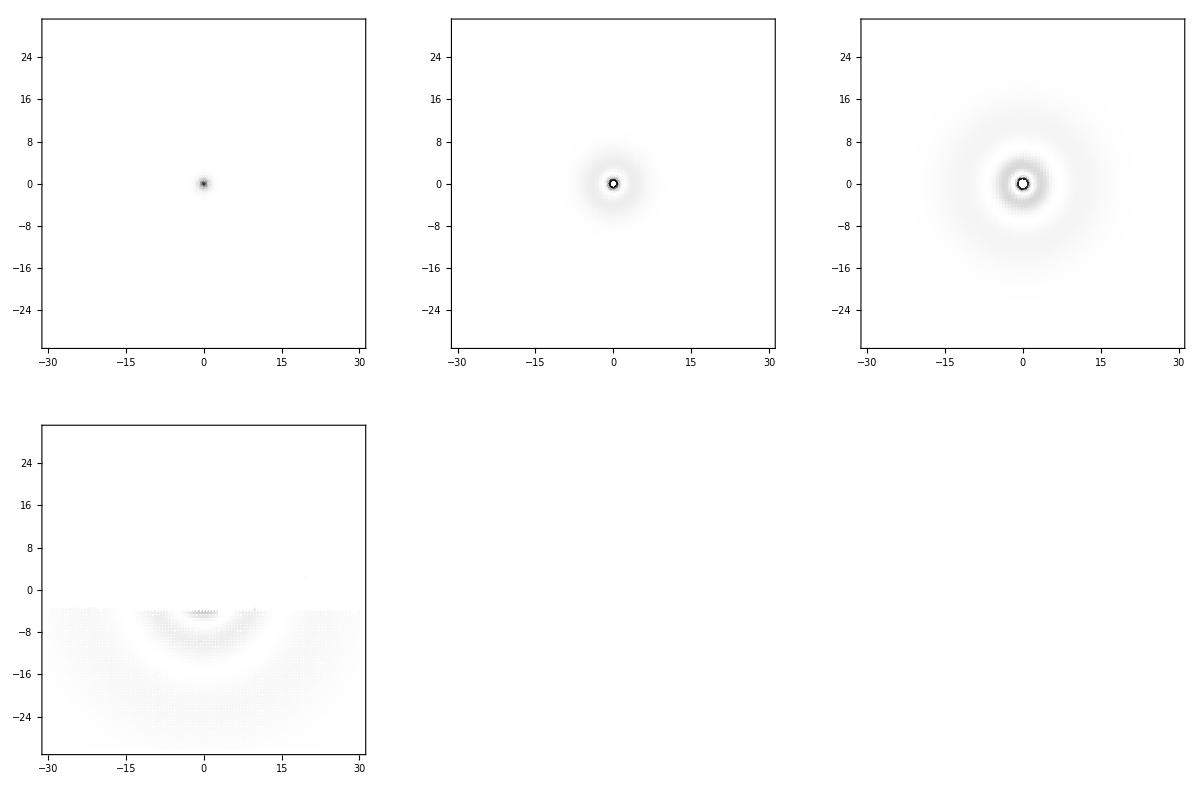

```mathematica
fig=GraphicsGrid[{Table[DensityPlot[(psi[n,Sqrt[x^2+y^2]])^2,{x,-30,30},{y,-30,30},PlotRange->{0,1},PlotPoints->100,ColorFunction -> Function[{z}, GrayLevel[1-z]], ColorFunctionScaling -> True, MaxRecursion -> 10],{n,1,3}],Table[DensityPlot[(psi[n,Sqrt[x^2+y^2]])^2,{x,-30,30},{y,-30,30},PlotRange->{0,1},PlotPoints->100,ColorFunction -> Function[{z}, GrayLevel[1-z]], ColorFunctionScaling -> True, MaxRecursion -> 10],{n,4,6}]}]
```

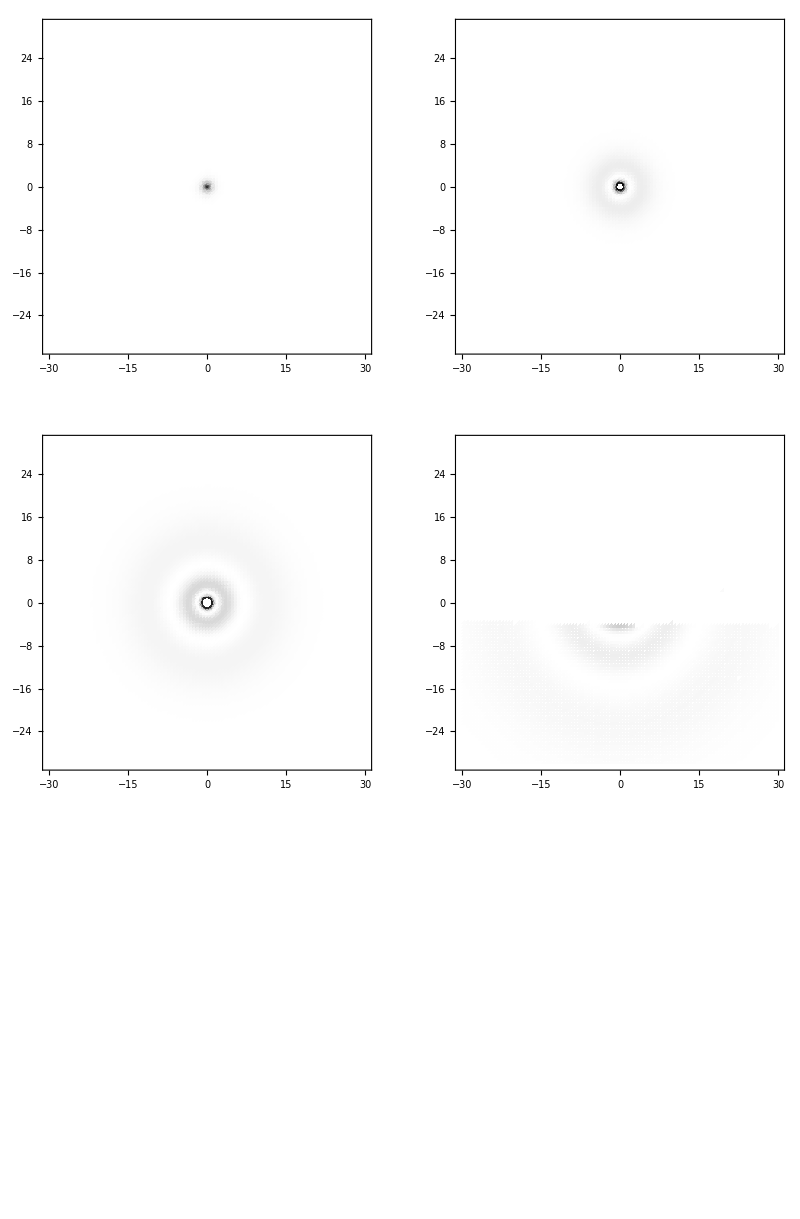

```mathematica
fig2=GraphicsGrid[{Table[DensityPlot[(psi[n,Sqrt[x^2+y^2]])^2,{x,-30,30},{y,-30,30},PlotRange->{0,1},PlotPoints->100,ColorFunction -> Function[{z}, GrayLevel[1-z]], ColorFunctionScaling -> True, MaxRecursion -> 10],{n,1,2}],
Table[DensityPlot[(psi[n,Sqrt[x^2+y^2]])^2,{x,-30,30},{y,-30,30},PlotRange->{0,1},PlotPoints->100,ColorFunction -> Function[{z}, GrayLevel[1-z]], ColorFunctionScaling -> True, MaxRecursion -> 10],{n,3,4}],Table[DensityPlot[(psi[n,Sqrt[x^2+y^2]])^2,{x,-30,30},{y,-30,30},PlotRange->{0,1},PlotPoints->100,ColorFunction -> Function[{z}, GrayLevel[1-z]], ColorFunctionScaling -> True, MaxRecursion -> 10],{n,5,6}]}]
```

```mathematica
fig=-Graphics-
```

-Graphics-

```mathematica
?Grid
```

Grid[{{expr_11,expr_12,…},{expr_21,expr_22,…},…}] is an object that formats with the expr_ij arranged in a two-dimensional grid.

```mathematica
?DensityPlot
```

DensityPlot[f,{x,x_min,x_max},{y,y_min,y_max}] makes a density plot of f as a function of x and y.

#### actual file saving part

```mathematica
Export["densityplots.png",fig]
```

densityplots.png

```mathematica
Export["artdensityplots.pdf",fig2]
```

artdensityplots.PDF

### Hydrogen V_eff

```mathematica
V[r_]:=n^2/2*1/r^2 - 1/r
```

```mathematica
Plot[Table[V[r]/.{n->i},{i,1,5}],{r,0,80},PlotRange->{-0.13,0.02},AxesLabel->{"ρ","V_eff"},PlotStyle->Black]
```

```mathematica
Plot[V[r]/.{n->5},{r,0,100}]
```

-Graphics-

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

### Yukawa Cutoff

```mathematica
Show[PolarPlot[{1,4,9},{th,0,2π},PlotStyle->{Gray},AxesLabel->"ρ"],PolarPlot[6.25,{th,0,2π},PlotStyle->{Black,Thick,Dashed}]]
```

### Yukawa Veff

```mathematica
V[r_,n_]:=n^2*1/r^2 - 2/r*ⅇ^(-r/l)
```

```mathematica
Show[Plot[Table[V[r,i]/.{l->8},{i,1,3}],{r,0,20},PlotRange->{-0.77,0.15},PlotStyle->Black,AxesLabel->{"ρ","V_eff"}],
ListPlot[minrs2,PlotStyle->Black,PlotMarkers->{Automatic,9}],
ListPlot[minvs2,PlotStyle->Black,PlotMarkers->{Automatic,9}],
Graphics[Text["n=1",{3.9,-0.25},Background->White,BaseStyle->Medium]],
Graphics[Text["n=2",{7,-0.0388},Background->White, BaseStyle->Medium]],
Graphics[Text["n=3",{9.3,0.0384},Background->White, BaseStyle->Medium]]
]
```

-Graphics-

```mathematica
Show[Plot[Table[V[r,i]/.{l->32},{i,1,6}],{r,0,150},PlotRange->{-0.03,0.005},AxesLabel->{"ρ","V_eff"},PlotStyle->Black],ListPlot[minrs,PlotStyle->Black,PlotMarkers->{Automatic,9}],
ListPlot[minvs,PlotStyle->Black,PlotMarkers->{Automatic,9}],
Graphics[Text["n=1",{31,-0.024},Background->White,BaseStyle->Medium]],
Graphics[Text["n=2",{31.75,-0.019},Background->White, BaseStyle->Medium]],
Graphics[Text["n=3",{35,-0.01215},Background->White, BaseStyle->Medium]],
Graphics[Text["n=4",{45,-0.00296},Background->White, BaseStyle->Medium]],
Graphics[Text["n=5",{60,0.00184},Background->White, BaseStyle->Medium]],
Graphics[Text["n=6",{72,0.00397},Background->White, BaseStyle->Medium]]]
```

-Graphics-

```mathematica
mins=Table[NMinimize[V[r,i]/.{l->32},r],{i,1,5}]
```

{{-0.938467,{r→1.00048}},{-0.191262,{r→4.02938}},{-0.0567589,{r→9.327}},{-0.0139266,{r→17.9646}},{0.00125181,{r→36.602}}}

```mathematica
minrs=Table[{r/.mins[[i,2]],0},{i,1,5}]
```

{{1.00048,0},{4.02938,0},{9.327,0},{17.9646,0},{36.602,0}}

```mathematica
minvs=Table[{0,mins[[i,1]]},{i,1,5}]
```

{{0,-0.938467},{0,-0.191262},{0,-0.0567589},{0,-0.0139266},{0,0.00125181}}

```mathematica
mins2=Table[NMinimize[V[r,i]/.{l->8},r],{i,1,2}]
```

{{-0.765046,{r→1.00735}},{-0.0557066,{r→4.49115}}}

```mathematica
minrs2=Table[{r/.mins2[[i,2]],0},{i,1,2}]
```

{{1.00735,0},{4.49115,0}}

```mathematica
minvs2=Table[{0,mins2[[i,1]]},{i,1,2}]
```

{{0,-0.765046},{0,-0.0557066}}

```mathematica
Lambdas={(ⅇ/2.),(4./((1+√5)(3+√5)(ⅇ^(-(1+√5)/2))))}
```

{1.35914,1.19053}

```mathematica
Lambdas[[2]]*9
```

10.7148

```mathematica
4./((1+√5)(3+√5)(ⅇ^(-(1+√5)/2)))
```

1.19053

```mathematica
Clear[l]
```

```mathematica
Plot[Table[V[r,1]/.{l->Lambdas[[i]]},{i,1,2}],{r,0,10}]
```

-Graphics-

```mathematica
nsquared[r_] := (r+r^2/l)ⅇ^(-r/l)
```

```mathematica
l=2
```

2

```mathematica
Plot[{nsquared[(1+√5)],nsquared[r]},{r,0,15},PlotRange->{0,2},PlotStyle->{{Black,Dashed},Black},AxesLabel->{"ρ_0","n^2"}]
```

-Graphics-

## Numeric Wave Functions

#### Large Yukawa

```mathematica
λ=200;
```

```mathematica
dρ=0.1;
ρinf=Round[20*λ];
nn=Round[ρinf/dρ];
```

```mathematica
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
```

```mathematica
valvecs200=Eigensystem[H,-100];
```

```mathematica
sorted=Sort[valvecs200[[1]]]
```

{-0.00487541,-0.00301651,-0.00178452,-0.00097922,-0.000472414,-0.00017815,-0.0000359636,4.60923×10^-7,2.73965×10^-6,7.0553×10^-6,0.0000132512,0.0000212167,0.000030878,0.0000421828,0.0000550911,0.0000695714,0.0000855979,0.000103149,0.000122206,0.000142753,0.000164776,0.000188262,0.0002132,0.00023958,0.000267393,0.00029663,0.000327283,0.000359345,0.000392809,0.00042767,0.000463922,0.000501559,0.000540576,0.000580969,0.000622732,0.000665863,0.000710356,0.000756209,0.000803417,0.000851977,0.000901887,0.000953142,0.00100574,0.00105968,0.00111496,0.00117157,0.00122951,0.00128878,0.00134939,0.00141132,0.00147457,0.00153914,0.00160503,0.00167225,0.00174077,0.00181062,0.00188177,0.00195424,0.00202802,0.0021031,0.00217949,0.00225719,0.00233619,0.0024165,0.00249811,0.00258101,0.00266522,0.00275072,0.00283752,0.00292562,0.00301501,0.00310569,0.00319767,0.00329094,0.0033855,0.00348135,0.00357849,0.00367692,0.00377663,0.00387763,0.00397992,0.00408349,0.00418834,0.00429448,0.0044019,0.0045106,0.00462058,0.00473185,0.00484439,0.00495821,0.00507331,0.00518969,0.00530735,0.00542628,0.00554649,0.00566797,0.00579073,0.00591476,0.00604007,0.00616665}

```mathematica
Position[valvecs200[[1]],sorted[[6]]]
```

{{85}}

```mathematica
Table[{i,1./i^2},{i,1,20}]
```

{{1,1.},{2,0.25},{3,0.111111},{4,0.0625},{5,0.04},{6,0.0277778},{7,0.0204082},{8,0.015625},{9,0.0123457},{10,0.01},{11,0.00826446},{12,0.00694444},{13,0.00591716},{14,0.00510204},{15,0.00444444},{16,0.00390625},{17,0.00346021},{18,0.00308642},{19,0.00277008},{20,0.0025}}

```mathematica
Show[Plot[1/150 psi[14,r],{r,0,700},PlotStyle->{Darker[Red],Thick}], ListPlot[Table[{i/10, 10/i valvecs200[[2,85,i]]},{i,1,7000}]]]
```

-Graphics-

```mathematica
Integrate[psi[2,r]^2,{r,0,∞}]
```

2

```mathematica
Show[Plot[psi[11,r],{r,0,50},PlotRange->{-0.05,0.05}], ListPlot[Table[{i/10, valvecs[[2,48,i]]},{i,1,500}]]]
```

-Graphics-

```mathematica
ListPlot[Table[{i/10, valvecs[[2,72,i]]},{i,1,500}],PlotRange->Full]
```

-Graphics-

#### A scattering state becomes a bound state

λ = 12.5 (scattering), ρinf = 20*λ

```mathematica
λ=14;
```

```mathematica
dρ=0.1;
ρinf=Round[20*λ];
nn=Round[ρinf/dρ];
```

```mathematica
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
```

```mathematica
valvecs3=Eigensystem[H,-100];
```

```mathematica
valvecs0[[1,100]]
```

0.0000793164

```mathematica
ListPlot[Table[{i/10, 10/i valvecs0[[2,100,i]]},{i,1,Length[valvecs0[[2,100]]]}],Joined->True]
```

-Graphics-

λ = 12.9 (scattering)

```mathematica
ListPlot[Table[{i/10,10/i valvecs[[2,100,i]]},{i,1,Length[valvecs[[2,100]]]}],Joined->True]
```

-Graphics-

λ = 13.1 (bound)

```mathematica
ListPlot[Table[{i/10, -10/i valvecs2[[2,100,i]]},{i,1,Length[valvecs2[[2,100]]]}],Joined->True]
```

-Graphics-

λ=14 (bound)

```mathematica
ListPlot[Table[{i/10, -10/i valvecs3[[2,99,i]]},{i,1,Length[valvecs3[[2,99]]]}],Joined->True]
```

-Graphics-

```mathematica
a=-Graphics-
```

-Graphics-

```mathematica
Show[Plot[-1/2 psi[4,r],{r,0,250},PlotRange->{-0.04,0.05}],a]
```

-Graphics-

```mathematica
ListPlot[Table[{i/10, valvecs3[[2,99,i]]},{i,1,100}]]
```

-Graphics-

#### The Importance of dρ

```mathematica
ListPlot[Table[{i/10, valvecs50[[2,93,i]]},{i,1,Length[valvecs50[[2,93]]]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListPlot[Table[{i/10, valvecs50[[2,93,i]]},{i,1,1000}]]
```

-Graphics-

#### The Importance of ρinf

12.5, scattering

```mathematica
ListPlot[Table[{i/10, bigvalvecs0[[2,100,i]]},{i,1,Length[bigvalvecs0[[2,100]]]}]]
```

-Graphics-

12.9, *bound*

```mathematica
ListPlot[Table[{i/10, bigvalvecs[[2,100,i]]},{i,1,Length[bigvalvecs[[2,100]]]}]]
```

-Graphics-

#### Plots for old things (λ=10)

```mathematica
ListPlot[Table[{i/10, valvecs[[2,43,i]]},{i,1,Length[valvecs[[2,43]]]}]]
```

-Graphics-

```mathematica
ListPlot[Table[{i/10, valvecs[[2,96,i]]},{i,1,Length[valvecs[[2,96]]]}],PlotRange->Full]
```

-Graphics-

```mathematica
ListPlot[Table[{i/10, valvecs[[2,100,i]]},{i,1,Length[valvecs[[2,100]]]}],PlotRange->Full]
```

-Graphics-

#### n = 2 bound states

```mathematica
λ=20;
```

```mathematica
dρ=0.1;
ρinf=Round[20*λ];
nn=Round[ρinf/dρ];
```

```mathematica
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
```

```mathematica
valvecs=Eigensystem[H,-150];
```

```mathematica
sorted=Sort[valvecs[[1]]]
```

{-0.901151,-0.163391,-0.0386787,-0.00617771,0.0000102392,0.000185522,0.000524666,0.00101988,0.00166517,0.00245646,0.00339078,0.00446578,0.00567958,0.00703062,0.0085176,0.0101394,0.0118951,0.0137839,0.0158051,0.0179581,0.0202423,0.0226572,0.0252023,0.0278774,0.0306819,0.0336157,0.0366783,0.0398695,0.043189,0.0466367,0.0502122,0.0539154,0.057746,0.061704,0.0657891,0.0700011,0.07434,0.0788056,0.0833977,0.0881163,0.0929611,0.0979321,0.103029,0.108252,0.113601,0.119076,0.124677,0.130403,0.136255,0.142232,0.148335,0.154562,0.160916,0.167394,0.173998,0.180726,0.18758,0.194559,0.201662,0.208891,0.216244,0.223722,0.231325,0.239052,0.246904,0.254881,0.262982,0.271208,0.279558,0.288033,0.296632,0.305355,0.314203,0.323175,0.332272,0.341492,0.350837,0.360306,0.369899,0.379616,0.389458,0.399423,0.409512,0.419726,0.430063,0.440525,0.45111,0.461819,0.472652,0.483609,0.49469,0.505894,0.517223,0.528675,0.540251,0.55195,0.563773,0.57572,0.587791,0.599985,0.612303,0.624744,0.637309,0.649998,0.66281,0.675746,0.688805,0.701987,0.715293,0.728723,0.742276,0.755952,0.769752,0.783675,0.797721,0.811891,0.826184,0.8406,0.85514,0.869803,0.884589,0.899498,0.914531,0.929687,0.944966,0.960368,0.975893,0.991541,1.00731,1.02321,1.03923,1.05537,1.07163,1.08802,1.10453,1.12116,1.13791,1.15479,1.1718,1.18892,1.20617,1.22354,1.24103,1.25865,1.27639,1.29425,1.31223,1.33034,1.34857,1.36692}

```mathematica
Position[valvecs[[1]],sorted[[2]]]
```

{{99}}

```mathematica
yuk=ListPlot[Table[{i/10, valvecs[[2,99,i]]},{i,1,300}],PlotRange->Full]
```

-Graphics-

```mathematica
yukpsi=ListPlot[Table[{i/10, valvecs[[2,99,i]]/i},{i,1,300}],PlotRange->Full,PlotStyle->{Black,Thick}]
```

-Graphics-

```mathematica
hydpsi=Plot[1/100 psi[2,r],{r,0,30},PlotRange->Full,PlotStyle->{Gray}]
```

-Graphics-

```mathematica
Show[yukpsi,hydpsi]
```

-Graphics-

```mathematica
hyd=Plot[1/7 r*psi[2,r],{r,0,30},PlotRange->Full,PlotStyle->{Red,Thick}]
```

-Graphics-

```mathematica
Show[yuk,hyd]
```

-Graphics-

## Error Analysis

```mathematica
l=0;
```

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
Critical[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Round[consts[[2]]];
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]]; (*Again, lets you know it's working/progress*)
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
Findlc[input_,i_,eps_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[i]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{0.1,input[[2]],input[[2]]/0.1}];
vah=Critical[input[[4]],{0.1,input[[2]],input[[2]]/0.1}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={input[[1]],Bisect[Critical,{0.1,input[[2]],input[[2]]/0.1},input[[3]],input[[4]],eps]};
,(*else*)
Print["Fail!"];
res={input[[1]],Null};
];
Return[res]
]
```

```mathematica
asymtote=Table[Findlc[{i,10.*2^(i-1)*13,range[[1]]-1,range[[2]]+1},i,10^-6],{i,1,6}]
```

***Beginning to calculate the 1th lambda, part 1

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 14.1255

Bisecting. Midpoint is 13.7546

Bisecting. Midpoint is 13.5692

Bisecting. Midpoint is 13.4765

Bisecting. Midpoint is 13.4301

Bisecting. Midpoint is 13.407

Bisecting. Midpoint is 13.4186

Bisecting. Midpoint is 13.4128

Bisecting. Midpoint is 13.4157

Bisecting. Midpoint is 13.4171

Bisecting. Midpoint is 13.4164

Bisecting. Midpoint is 13.416

Bisecting. Midpoint is 13.4158

Bisecting. Midpoint is 13.4159

Bisecting. Midpoint is 13.416

Bisecting. Midpoint is 13.416

Bisecting. Midpoint is 13.416

«5 more identical outputs»

***Beginning to calculate the 2th lambda, part 2

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 12.9202

Bisecting. Midpoint is 12.9666

Bisecting. Midpoint is 12.9898

Bisecting. Midpoint is 12.9782

Bisecting. Midpoint is 12.984

Bisecting. Midpoint is 12.9869

Bisecting. Midpoint is 12.9883

Bisecting. Midpoint is 12.9876

Bisecting. Midpoint is 12.9872

Bisecting. Midpoint is 12.9874

Bisecting. Midpoint is 12.9875

Bisecting. Midpoint is 12.9875

Bisecting. Midpoint is 12.9876

Bisecting. Midpoint is 12.9876

Bisecting. Midpoint is 12.9876

«4 more identical outputs»

***Beginning to calculate the 3th lambda, part 3

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 12.7812

Bisecting. Midpoint is 12.8043

Bisecting. Midpoint is 12.8159

Bisecting. Midpoint is 12.8217

Bisecting. Midpoint is 12.8246

Bisecting. Midpoint is 12.8261

Bisecting. Midpoint is 12.8253

Bisecting. Midpoint is 12.8257

Bisecting. Midpoint is 12.8255

Bisecting. Midpoint is 12.8254

Bisecting. Midpoint is 12.8255

Bisecting. Midpoint is 12.8255

Bisecting. Midpoint is 12.8255

«5 more identical outputs»

***Beginning to calculate the 4th lambda, part 4

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 12.7812

Bisecting. Midpoint is 12.758

Bisecting. Midpoint is 12.7464

Bisecting. Midpoint is 12.7522

Bisecting. Midpoint is 12.7551

Bisecting. Midpoint is 12.7536

Bisecting. Midpoint is 12.7544

Bisecting. Midpoint is 12.754

Bisecting. Midpoint is 12.7542

Bisecting. Midpoint is 12.7543

Bisecting. Midpoint is 12.7543

Bisecting. Midpoint is 12.7543

«6 more identical outputs»

***Beginning to calculate the 5th lambda, part 5

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 12.7116

Bisecting. Midpoint is 12.7232

Bisecting. Midpoint is 12.7174

Bisecting. Midpoint is 12.7203

Bisecting. Midpoint is 12.7218

Bisecting. Midpoint is 12.721

Bisecting. Midpoint is 12.7207

Bisecting. Midpoint is 12.7209

Bisecting. Midpoint is 12.7208

Bisecting. Midpoint is 12.7208

Bisecting. Midpoint is 12.7208

«6 more identical outputs»

***Beginning to calculate the 6th lambda, part 6

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 12.7116

Bisecting. Midpoint is 12.7

Bisecting. Midpoint is 12.7058

Bisecting. Midpoint is 12.7029

Bisecting. Midpoint is 12.7044

Bisecting. Midpoint is 12.7051

Bisecting. Midpoint is 12.7047

Bisecting. Midpoint is 12.7046

Bisecting. Midpoint is 12.7047

Bisecting. Midpoint is 12.7046

Bisecting. Midpoint is 12.7046

Bisecting. Midpoint is 12.7046

«5 more identical outputs»

{{1,{13.416,2,3}},{2,{12.9876,1,2}},{3,{12.8255,1,2}},{4,{12.7543,0,1}},{5,{12.7208,0,1}},{6,{12.7046,0,1}}}

```mathematica
asymtote=Join[asymtote,Table[Findlc[{i,10.*2^(i-1)*13,range[[1]]-1,range[[2]]+1},i,10^-6],{i,7,8}]]
```

***Beginning to calculate the 7th lambda, part 7

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 12.7116

Bisecting. Midpoint is 12.7

Bisecting. Midpoint is 12.6942

Bisecting. Midpoint is 12.6971

Bisecting. Midpoint is 12.6957

Bisecting. Midpoint is 12.6964

Bisecting. Midpoint is 12.6968

Bisecting. Midpoint is 12.6966

Bisecting. Midpoint is 12.6967

Bisecting. Midpoint is 12.6966

Bisecting. Midpoint is 12.6966

Bisecting. Midpoint is 12.6966

«5 more identical outputs»

***Beginning to calculate the 8th lambda, part 8

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 12.7116

Bisecting. Midpoint is 12.7

Bisecting. Midpoint is 12.6942

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6928

Bisecting. Midpoint is 12.6921

Bisecting. Midpoint is 12.6924

Bisecting. Midpoint is 12.6926

Bisecting. Midpoint is 12.6927

Bisecting. Midpoint is 12.6927

Bisecting. Midpoint is 12.6926

Bisecting. Midpoint is 12.6926

Bisecting. Midpoint is 12.6927

Bisecting. Midpoint is 12.6927

Bisecting. Midpoint is 12.6927

«2 more identical outputs»

{{1,{13.416,2,3}},{2,{12.9876,1,2}},{3,{12.8255,1,2}},{4,{12.7543,0,1}},{5,{12.7208,0,1}},{6,{12.7046,0,1}},{7,{12.6966,0,1}},{8,{12.6927,0,1}}}

```mathematica
asymtote
```

{{1,{13.416,2,3}},{2,{12.9876,1,2}},{3,{12.8255,1,2}},{4,{12.7543,0,1}},{5,{12.7208,0,1}},{6,{12.7046,0,1}},{7,{12.6966,0,1}},{8,{12.6927,0,1}}}

```mathematica
asymtotic=Table[{2^(i-1),asymtote[[i,2,1]]},{i,1,Length[asymtote]}]
```

{{1,13.416},{2,12.9876},{4,12.8255},{8,12.7543},{16,12.7208},{32,12.7046},{64,12.6966},{128,12.6927}}

```mathematica
Show[ListPlot[asymtotic,AxesOrigin->{0,12.6},PlotMarkers->{Automatic,6},PlotStyle->{Black},Joined->True]]
```

-Graphics-

```mathematica
range={12.900390625,13.8671875};
```

```mathematica
r1d1 = Bisect[Critical,{0.1,40.*13},range[[1]]-1,range[[2]]+1,10^-6]
```

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 12.7812

Bisecting. Midpoint is 12.8043

Bisecting. Midpoint is 12.8159

Bisecting. Midpoint is 12.8217

Bisecting. Midpoint is 12.8246

Bisecting. Midpoint is 12.8261

Bisecting. Midpoint is 12.8253

Bisecting. Midpoint is 12.8257

Bisecting. Midpoint is 12.8255

Bisecting. Midpoint is 12.8254

Bisecting. Midpoint is 12.8255

Bisecting. Midpoint is 12.8255

Bisecting. Midpoint is 12.8255

«5 more identical outputs»

{12.8255,1,2}

```mathematica
r2d1=Bisect[Critical,{0.1,80.*13},range[[1]]-1,range[[2]]+1,10^-6]
```

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 12.7812

Bisecting. Midpoint is 12.758

Bisecting. Midpoint is 12.7464

Bisecting. Midpoint is 12.7522

Bisecting. Midpoint is 12.7551

Bisecting. Midpoint is 12.7536

Bisecting. Midpoint is 12.7544

Bisecting. Midpoint is 12.754

Bisecting. Midpoint is 12.7542

Bisecting. Midpoint is 12.7543

Bisecting. Midpoint is 12.7543

Bisecting. Midpoint is 12.7543

«6 more identical outputs»

{12.7543,0,1}

```mathematica
r1d2=Bisect[Critical,{0.05,40.*13},range[[1]]-1,range[[2]]+1,10^-6]
```

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 12.7812

Bisecting. Midpoint is 12.8043

Bisecting. Midpoint is 12.8159

Bisecting. Midpoint is 12.8217

Bisecting. Midpoint is 12.8246

Bisecting. Midpoint is 12.8232

Bisecting. Midpoint is 12.8239

Bisecting. Midpoint is 12.8235

Bisecting. Midpoint is 12.8233

Bisecting. Midpoint is 12.8233

Bisecting. Midpoint is 12.8233

«7 more identical outputs»

{12.8233,1,2}

```mathematica
r2d2=Bisect[Critical,{0.05,80.*13},range[[1]]-1,range[[2]]+1,10^-6]
```

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 12.7812

Bisecting. Midpoint is 12.758

Bisecting. Midpoint is 12.7464

Bisecting. Midpoint is 12.7522

Bisecting. Midpoint is 12.7493

Bisecting. Midpoint is 12.7507

Bisecting. Midpoint is 12.7515

Bisecting. Midpoint is 12.7518

Bisecting. Midpoint is 12.752

Bisecting. Midpoint is 12.7521

Bisecting. Midpoint is 12.7521

Bisecting. Midpoint is 12.7521

«6 more identical outputs»

{12.7521,0,1}

```mathematica
Show[
ListPlot[{{1,r1d1[[1]]},{2,r2d1[[1]]}},PlotMarkers->{Automatic,Large},PlotRange->{12.74,12.85},AxesOrigin->{0.8,12.74},PlotStyle->Black,AxesLabel->{"","λ_c"}],
ListPlot[{{1,r1d1[[1]]},{2,r1d2[[1]]}},PlotRange->{12.74,12.85},AxesOrigin->{0.8,12.74},PlotMarkers->{Automatic,Medium},PlotStyle->Gray],
ListPlot[{{1,r2d1[[1]]},{2,r2d2[[1]]}},PlotRange->{12.74,12.85},AxesOrigin->{0.8,12.74},PlotMarkers->{Automatic,Medium},PlotStyle->Lighter[Gray]]
]
```

```mathematica
12.754289095522836-12.752123929327354
```

0.00216517

```mathematica
12.825492011150345-12.823324015596882
```

0.002168

```mathematica
ListPlot[{{1,r1d1[[1]]},{2,r1d2[[1]]}},PlotRange->{12.74,12.85},AxesOrigin->{0.8,12.74}]
```

-Graphics-

```mathematica
?PlotRange
```

PlotRange is an option for graphics functions that specifies what range of coordinates to include in a plot.

## Results

```mathematica
SetDirectory["~/Library/AFS@Reed/emcmanis/Thesis/Calculations/Angular Momentum/"]
```

/afs/reed.edu/user/e/m/emcmanis/Thesis/Calculations/Angular Momentum

```mathematica
l0=Import["l0.csv"];
l1=Import["l1.csv"];
l2=Import["l2.csv"];
l3=Import["l3.csv"];
l4=Import["l4.csv"];
l5=Import["l5.csv"];
l6=Import["l6.csv"];
l7=Import["l7.csv"];
l8=Import["l8.csv"];
l9=Import["l9.csv"];
l10=Import["l10.csv"];
```

```mathematica
SetDirectory["~/Library/AFS@Reed/emcmanis/Thesis/TeX/Thesis Template/Figures"]
```

/afs/reed.edu/user/e/m/emcmanis/Thesis/TeX/Thesis Template/Figures

```mathematica
l0
```

{{0.895295,0.0275888},{3.29715,0.0365915},{7.28782,0.0593562},{12.8273,0.0717554},{19.9501,0.0926809},{28.6423,0.113488},{38.9044,0.134234},{50.738,0.156292},{64.1418,0.178222},{79.116,0.200296},{95.6605,0.222144},{113.776,0.244337},{133.462,0.267039},{154.72,0.290463},{177.547,0.313196},{201.946,0.336596},{227.915,0.359412},{255.455,0.38285},{284.566,0.406629},{315.248,0.430092},{347.501,0.453882},{381.324,0.477747},{416.718,0.501977},{453.683,0.525859},{492.219,0.550117},{532.326,0.574412},{574.003,0.599027},{617.251,0.623271},{662.07,0.647825},{708.46,0.672426},{756.421,0.697392},{805.953,0.721938},{857.055,0.746843},{909.728,0.771789},{963.973,0.796995}}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ErrorListPlot[l0,AxesLabel->{"n","λ_n"}]
```

-Graphics-

```mathematica
loglog=Table[{Log[N[i]],Log[l0[[i,1]]],1/l0[[i,1]]*l0[[i,2]]},{i,1,Length[l0]}]
```

{{0.,-0.110602,0.0308154},{0.693147,1.19306,0.0110979},{1.09861,1.9862,0.00814458},{1.38629,2.55158,0.00559394},{1.60944,2.99323,0.00464564},{1.79176,3.35489,0.00396226},{1.94591,3.66111,0.00345036},{2.07944,3.92668,0.00308037},{2.19722,4.1611,0.00277856},{2.30259,4.37092,0.00253168},{2.3979,4.56081,0.00232221},{2.48491,4.73423,0.00214753},{2.56495,4.89382,0.00200086},{2.63906,5.04162,0.00187735},{2.70805,5.17924,0.00176402},{2.77259,5.308,0.00166676},{2.83321,5.42897,0.00157696},{2.89037,5.54305,0.0014987},{2.94444,5.65097,0.00142894},{2.99573,5.75336,0.0013643},{3.04452,5.85077,0.00130613},{3.09104,5.94365,0.00125286},{3.13549,6.03241,0.0012046},{3.17805,6.1174,0.00115909},{3.21888,6.19892,0.00111763},{3.2581,6.27726,0.00107906},{3.29584,6.35264,0.00104359},{3.3322,6.42528,0.00100975},{3.3673,6.49537,0.000978484},{3.4012,6.56309,0.000949137},{3.43399,6.6286,0.000921963},{3.46574,6.69202,0.000895757},{3.49651,6.7535,0.000871406},{3.52636,6.81315,0.000848373},{3.55535,6.87106,0.000826782}}

Using w_i = 1/Δi^2, from Taylor.

```mathematica
weights=Table[1/(loglog[[i,3]]^2),{i,1,Length[loglog]}];
```

This is also from Taylor, used below

```mathematica
Delta=Sum[weights[[i]],{i,Length[weights]}]*Sum[weights[[i]]*loglog[[i,1]]^2,{i,Length[loglog]}]-(Sum[weights[[i]]*loglog[[i,1]],{i,Length[loglog]}])^2;
```

More symbols to make expressions less unweildy.

```mathematica
x[i_]:=loglog[[i,1]];
y[i_]:=loglog[[i,2]];
w[i_]:=weights[[i]];
```

Now, the fit coefficients (for line off form y = A + Bx):

```mathematica
A=1/Delta(Sum[w[i]*x[i]^2,{i,Length[loglog]}]*Sum[w[i]*y[i],{i,Length[loglog]}]-Sum[w[i]*x[i],{i,Length[loglog]}]*Sum[w[i]*x[i]*y[i],{i,Length[loglog]}])
```

-0.22149

```mathematica
B=1/Delta(Sum[w[i],{i,Length[loglog]}]*Sum[w[i]*x[i]*y[i],{i,Length[loglog]}]-Sum[w[i]*x[i],{i,Length[loglog]}]*Sum[w[i]*y[i],{i,Length[loglog]}])
```

1.9947

Again, not quite quadratic. We can plot both:

```mathematica
F[x_]:=A+B*x
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Show[Plot[F[x],{x,1.,3.75}],ErrorListPlot[Table[{{x[i],y[i]},ErrorBar[loglog[[i,3]]]},{i,1,Length[loglog]}]]]
```

-Graphics-

Uncertainties in A and B:

```mathematica
σA=Sqrt[Sum[w[i]*x[i]^2,{i,Length[loglog]}]/Delta]
```

0.00206866

```mathematica
σB=Sqrt[Sum[w[i],{i,Length[loglog]}]/Delta]
```

0.000640333

This is the max value for B:

```mathematica
B+%22
```

{2.07695,1.87963}

Checking the goodness of the fit:

```mathematica
fitvals=Table[F[loglog[[i,1]]],{i,1,Length[loglog]}];
```

```mathematica
residuals=Table[fitvals[[i]]-loglog[[i,2]],{i,1,Length[loglog]}];
```

These look like a curve, not random, which kind of worries me a bit. That said, the fit looks okay.

```mathematica
ListPlot[residuals]
```

-Graphics-

## All the LCs -- Results

### Data Import

Set this to wherever this file is.

```mathematica
SetDirectory["~/Library/AFS@Reed/emcmanis/Thesis/Calculations/Angular Momentum/"]
```

/afs/reed.edu/user/e/m/emcmanis/Thesis/Calculations/Angular Momentum

```mathematica
l0=Import["l0.csv"];
l1=Import["l1.csv"];
l2=Import["l2.csv"];
l3=Import["l3.csv"];
l4=Import["l4.csv"];
l5=Import["l5.csv"];
l6=Import["l6.csv"];
l7=Import["l7.csv"];
l8=Import["l8.csv"];
l9=Import["l9.csv"];
l10=Import["l10.csv"];
```

```mathematica
ls={l0,l1,l2,l3,l4,l5,l6,l7,l8,l9,l10};
```

```mathematica
lsplot=Table[Table[{j,ls[[i,j,1]]},{j,1,Length[ls[[i]]]}],{i,1,Length[ls]}];
```

There are three data points missing here, as evidenced by the discontinuities in the curves. Instead of going back and taking these data points, I merely shifted the other data points one forward, to make the curves smooth again. The following loop does this.

```mathematica
For[i=22,i≤Length[lsplot[[3]]],i++,
lsplot[[3,i,1]]=i+1;
]
For[i=10,i≤Length[lsplot[[7]]],i++,
lsplot[[7,i,1]]=i+1;
]
For[i=19,i≤Length[lsplot[[6]]],i++,
lsplot[[6,i,1]]=i+1;
]
```

```mathematica
ListPlot[lsplot,AxesLabel->{"n","λ_n"}]
```

-Graphics-

```mathematica
l0[[1,1]]-l0[[1,2]]
```

0.867706

```mathematica
l0[[1]]
```

{0.895295,0.0275888}

```mathematica
1.190 612 27±0.000 000 04
```

```mathematica
1/(1.19061227+0.00000004)-1/(1.19061227+0.00000004)
```

0.

```mathematica
N[1/(1.19061227),9]
```

0.839904

```mathematica
?N
```

N[expr] gives the numerical value of expr. 
N[expr,n] attempts to give a result with n-digit precision.

```mathematica
(%26-%20)/(%20)*100
```

3.31012

### Least Squares Fit

Ls are in the form {n,l}

```mathematica
PolyFit[lambdas_]:=Module[{M,res},
M=({{Length[lambdas], Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^4,{i,1,Length[lambdas]}]}});
res=Inverse[M].{Sum[lambdas[[i,2]],{i,1,Length[lambdas]}],
Sum[lambdas[[i,1]]*lambdas[[i,2]],{i,1,Length[lambdas]}],
Sum[lambdas[[i,1]]^2*lambdas[[i,2]],{i,1,Length[lambdas]}]};
Return[{a->res[[1]],b->res[[2]],c->res[[3]]}]
]
```

```mathematica
DeltaYs[lambdas_,fit_]:=Sqrt[1/(Length[lambdas]-3)Sum[(lambdas[[i,2]]-(a+b lambdas[[i,1]]+c lambdas[[i,1]]^2)/.fit)^2,{i,1,Length[lambdas]}]]
```

```mathematica
DeltaABCs[lambdas_,fit_,dy_]:=Module[{M,res},
M=({{Length[lambdas], Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^4,{i,1,Length[lambdas]}]}});
res=Sqrt[Sum[(Inverse[M].{1,
lambdas[[i,1]],
lambdas[[i,1]]^2}*dy)^2,{i,1,Length[lambdas]}]];
Return[res]
]
```

```mathematica
Fits=Table[PolyFit[lsplot[[i]]],{i,1,Length[lsplot]}];
```

```mathematica
Fits[[1]]
```

{a→0.0578679,b→0.0517547,c→0.785389}

```mathematica
Show[Plot[(a + b x + c x^2)/.Fits[[1]],{x,0,36}],ListPlot[lsplot[[1]]]]
```

-Graphics-

```mathematica
dys=Table[DeltaYs[lsplot[[i]],Fits[[i]]],{i,1,Length[Fits]}];
```

```mathematica
l0[[1]]
```

{0.895295,0.0275888}

```mathematica
TableForm[Table[Join[{"l = "<>ToString[i-1]},Fits[[i]],{DeltaYs[lsplot[[i]],Fits[[i]]]}],{i,1,Length[Fits]}]]
```

l = 0 | a→0.0578679 | b→0.0517547 | c→0.785389 | 0.0018454
l = 1 | a→2.08389 | b→1.87181 | c→0.783359 | 0.061561
l = 2 | a→6.69367 | b→3.76342 | c→0.780961 | 0.100205
l = 3 | a→13.9713 | b→5.66987 | c→0.778668 | 0.126059
l = 4 | a→23.916 | b→7.58959 | c→0.776349 | 0.141452
l = 5 | a→36.5385 | b→9.51975 | c→0.774003 | 0.148965
l = 6 | a→51.8429 | b→11.4585 | c→0.771512 | 0.141571
l = 7 | a→69.8763 | b→13.3975 | c→0.769258 | 0.136714
l = 8 | a→90.6213 | b→15.3367 | c→0.767164 | 0.129699
l = 9 | a→114.081 | b→17.2771 | c→0.765162 | 0.12079
l = 10 | a→140.221 | b→19.2291 | c→0.762649 | 0.101198

```mathematica
dabcs=Table[DeltaABCs[lsplot[[i]],Fits[[i]],dys[[i]]],{i,1,Length[lsplot]}]
```

{{0.000991933,0.00012705,3.4233×10^-6},{0.0336319,0.00443055,0.000122796},{0.0569554,0.00800701,0.000234662},{0.0725534,0.0104523,0.000316912},{0.0829445,0.0123341,0.000386055},{0.0896912,0.0139121,0.000448679},{0.0881913,0.014648,0.000509933},{0.0870456,0.0148573,0.000534104},{0.0844883,0.0149742,0.000559067},{0.0805912,0.0148535,0.000576805},{0.0710914,0.0142391,0.000601176}}

```mathematica
dabcs//TableForm
```

0.000991933 | 0.00012705 | 3.4233×10^-6
0.0336319 | 0.00443055 | 0.000122796
0.0569554 | 0.00800701 | 0.000234662
0.0725534 | 0.0104523 | 0.000316912
0.0829445 | 0.0123341 | 0.000386055
0.0896912 | 0.0139121 | 0.000448679
0.0881913 | 0.014648 | 0.000509933
0.0870456 | 0.0148573 | 0.000534104
0.0844883 | 0.0149742 | 0.000559067
0.0805912 | 0.0148535 | 0.000576805
0.0710914 | 0.0142391 | 0.000601176

```mathematica
Fits[[11,3]]
```

c→0.762649

```mathematica
(c/.{Fits[[11,3]]})+dabcs[[11,3]]
```

0.763251

```mathematica
as=Table[{i-1,a/.Fits[[i,1]]},{i,1,Length[Fits]}]
```

{{0,0.0578679},{1,2.08389},{2,6.69367},{3,13.9713},{4,23.916},{5,36.5385},{6,51.8429},{7,69.8763},{8,90.6213},{9,114.081},{10,140.221}}

```mathematica
aserr=Table[{{i-1,a/.Fits[[i,1]]},ErrorBar[dabcs[[i,1]]]},{i,1,Length[Fits]}];
```

```mathematica
bs=Table[{i-1,b/.Fits[[i,2]]},{i,1,Length[Fits]}]
```

{{0,0.0517547},{1,1.87181},{2,3.76342},{3,5.66987},{4,7.58959},{5,9.51975},{6,11.4585},{7,13.3975},{8,15.3367},{9,17.2771},{10,19.2291}}

```mathematica
bserr=Table[{{i-1,b/.Fits[[i,2]]},ErrorBar[dabcs[[i,2]]]},{i,1,Length[Fits]}];
```

```mathematica
cs=Table[{i-1,c/.Fits[[i,3]]},{i,1,Length[Fits]}]
```

{{0,0.785389},{1,0.783359},{2,0.780961},{3,0.778668},{4,0.776349},{5,0.774003},{6,0.771512},{7,0.769258},{8,0.767164},{9,0.765162},{10,0.762649}}

```mathematica
cserr=Table[{{i-1,c/.Fits[[i,3]]},ErrorBar[dabcs[[i,3]]]},{i,1,Length[Fits]}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
?ErrorBarPlots
```

Information::notfound: Symbol "ErrorBarPlots" not found.

```mathematica
ErrorListPlot[aserr]
```

-Graphics-

```mathematica
ErrorListPlot[bserr]
```

-Graphics-

```mathematica
ErrorListPlot[cserr]
```

-Graphics-